```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)+Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^+a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^+a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^+a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^+a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^+a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^+a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^+a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^+a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^+a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)+(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)+(3 𝒿-U) (a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^+a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^+a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^+a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^+a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^+a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^+a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^+a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^+a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)+𝒿 (a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^+a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)-U (a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^+a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^+a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^+a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^+a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^+a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.5,cj->U/5,U->6,t23->x t22,t22->0.3}
```

{Δ→0.5,𝒿→U/5,U→6,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,2,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,2,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,2,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,2,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,2,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,2,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,2,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,2,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,2,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,2,0.2}];
```

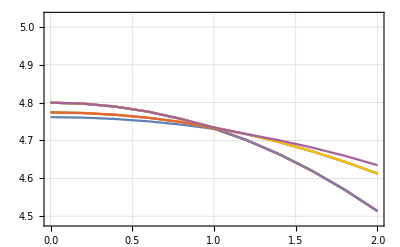

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,2,0.1}],{j,1,10}]
```

1

1.66192×10^-17

1

0.0000790843

1

0.000316619

1

0.000713445

1

0.00127096

1

0.0019911

1

0.00287632

1

0.00392958

1

0.0051543

1

0.00655436

1

0.00813398

1

5.89172

1

5.86796

1

5.84136

1

5.81193

1

5.77972

1

5.74483

1

5.70744

1

5.66778

1

5.62613

1

5.5828

2

2.

2

1.9999

2

1.9996

2

1.99909

2

1.99837

2

1.99744

2

1.99629

2

1.99492

2

1.9933

2

1.99144

2

5.91271

2

5.89172

2

5.86796

2

5.84136

2

5.81193

2

5.77972

2

5.74483

2

5.70744

2

5.66778

2

5.62613

2

5.5828

3

2.

3

1.9999

3

1.9996

3

1.99909

3

1.99837

3

1.99744

3

1.99629

3

1.99492

3

1.9933

3

1.99144

3

5.91271

3

5.89172

3

5.86796

3

5.84136

3

5.81193

3

5.77972

3

5.74483

3

5.70744

3

5.66778

3

5.62613

3

5.5828

4

2.

4

1.9999

4

1.9996

4

1.99909

4

1.99837

4

1.99744

4

1.99629

4

1.99492

4

1.9933

4

1.99144

4

5.91271

4

5.89172

4

5.86796

4

5.84136

4

5.81193

4

5.77972

4

5.74483

4

5.70744

4

5.66778

4

5.62613

4

5.5828

5

6.

5

5.99925

5

5.997

5

5.99318

5

5.98772

5

5.98049

5

5.97137

5

5.9602

5

5.9468

5

5.93103

5

5.91271

5

5.89172

5

5.86796

5

5.84136

5

5.81193

5

5.77972

5

5.74483

5

5.70744

5

5.66778

5

5.62613

5

5.5828

6

6.

6

5.99925

6

5.997

6

5.99318

6

5.98772

6

5.98049

6

5.97137

6

5.9602

6

5.9468

6

5.93103

6

5.91271

6

0.00989775

6

1.98423

6

1.98124

6

1.97793

6

1.97429

6

1.97028

6

1.96591

6

1.96115

6

1.95598

6

1.95038

7

6.

7

5.99925

7

5.997

7

5.99318

7

5.98772

7

5.98049

7

5.97137

7

5.9602

7

5.9468

7

5.93103

7

1.98931

7

1.98692

7

1.98423

7

1.98124

7

1.97793

7

1.97429

7

1.97028

7

1.96591

7

1.96115

7

1.95598

7

1.95038

8

6.

8

5.99925

8

5.997

8

5.99318

8

5.98772

8

5.98049

8

5.97137

8

5.9602

8

5.9468

8

5.93103

8

1.98931

8

1.98692

8

1.98423

8

1.98124

8

1.97793

8

1.97429

8

1.97028

8

1.96591

8

1.96115

8

1.95598

8

1.95038

9

6.

9

5.99925

9

5.997

9

5.99318

9

5.98772

9

5.98049

9

5.97137

9

5.9602

9

5.9468

9

5.93103

9

1.98931

9

1.98692

9

0.0118505

9

0.0139973

9

0.0163432

9

0.0188935

9

0.0216531

9

0.0246268

9

0.0278193

9

0.0312344

9

0.0348755

10

0.75

10

0.749982

10

0.749928

10

0.749839

10

0.749715

10

0.749556

10

0.749363

10

0.749137

10

0.74888

10

0.748592

10

0.748275

10

0.74793

10

0.747559

10

0.747164

10

0.746745

10

0.746306

10

0.745847

10

0.745371

10

0.74488

10

0.744376

10

0.74386

```mathematica
data1//MatrixForm
```

(1 | 0. | 1.66192×10^-17 | 4.76167
1 | 0.1 | 0.0000790843 | 4.76137
1 | 0.2 | 0.000316619 | 4.76044
1 | 0.3 | 0.000713445 | 4.7589
1 | 0.4 | 0.00127096 | 4.75675
1 | 0.5 | 0.0019911 | 4.75397
1 | 0.6 | 0.00287632 | 4.75057
1 | 0.7 | 0.00392958 | 4.74654
1 | 0.8 | 0.0051543 | 4.74188
1 | 0.9 | 0.00655436 | 4.73659
1 | 1. | 0.00813398 | 4.73066
1 | 1.1 | 5.89172 | 4.7171
1 | 1.2 | 5.86796 | 4.70081
1 | 1.3 | 5.84136 | 4.68295
1 | 1.4 | 5.81193 | 4.6635
1 | 1.5 | 5.77972 | 4.64246
1 | 1.6 | 5.74483 | 4.61982
1 | 1.7 | 5.70744 | 4.59558
1 | 1.8 | 5.66778 | 4.56975
1 | 1.9 | 5.62613 | 4.54236
1 | 2. | 5.5828 | 4.51343
2 | 0. | 2. | 4.7742
2 | 0.1 | 1.9999 | 4.7738
2 | 0.2 | 1.9996 | 4.77261
2 | 0.3 | 1.99909 | 4.77063
2 | 0.4 | 1.99837 | 4.76785
2 | 0.5 | 1.99744 | 4.76427
2 | 0.6 | 1.99629 | 4.75989
2 | 0.7 | 1.99492 | 4.75471
2 | 0.8 | 1.9933 | 4.74873
2 | 0.9 | 1.99144 | 4.74194
2 | 1. | 5.91271 | 4.73185
2 | 1.1 | 5.89172 | 4.7171
2 | 1.2 | 5.86796 | 4.70081
2 | 1.3 | 5.84136 | 4.68295
2 | 1.4 | 5.81193 | 4.6635
2 | 1.5 | 5.77972 | 4.64246
2 | 1.6 | 5.74483 | 4.61982
2 | 1.7 | 5.70744 | 4.59558
2 | 1.8 | 5.66778 | 4.56975
2 | 1.9 | 5.62613 | 4.54236
2 | 2. | 5.5828 | 4.51343
3 | 0. | 2. | 4.7742
3 | 0.1 | 1.9999 | 4.7738
3 | 0.2 | 1.9996 | 4.77261
3 | 0.3 | 1.99909 | 4.77063
3 | 0.4 | 1.99837 | 4.76785
3 | 0.5 | 1.99744 | 4.76427
3 | 0.6 | 1.99629 | 4.75989
3 | 0.7 | 1.99492 | 4.75471
3 | 0.8 | 1.9933 | 4.74873
3 | 0.9 | 1.99144 | 4.74194
3 | 1. | 5.91271 | 4.73185
3 | 1.1 | 5.89172 | 4.7171
3 | 1.2 | 5.86796 | 4.70081
3 | 1.3 | 5.84136 | 4.68295
3 | 1.4 | 5.81193 | 4.6635
3 | 1.5 | 5.77972 | 4.64246
3 | 1.6 | 5.74483 | 4.61982
3 | 1.7 | 5.70744 | 4.59558
3 | 1.8 | 5.66778 | 4.56975
3 | 1.9 | 5.62613 | 4.54236
3 | 2. | 5.5828 | 4.51343
4 | 0. | 2. | 4.7742
4 | 0.1 | 1.9999 | 4.7738
4 | 0.2 | 1.9996 | 4.77261
4 | 0.3 | 1.99909 | 4.77063
4 | 0.4 | 1.99837 | 4.76785
4 | 0.5 | 1.99744 | 4.76427
4 | 0.6 | 1.99629 | 4.75989
4 | 0.7 | 1.99492 | 4.75471
4 | 0.8 | 1.9933 | 4.74873
4 | 0.9 | 1.99144 | 4.74194
4 | 1. | 5.91271 | 4.73185
4 | 1.1 | 5.89172 | 4.7171
4 | 1.2 | 5.86796 | 4.70081
4 | 1.3 | 5.84136 | 4.68295
4 | 1.4 | 5.81193 | 4.6635
4 | 1.5 | 5.77972 | 4.64246
4 | 1.6 | 5.74483 | 4.61982
4 | 1.7 | 5.70744 | 4.59558
4 | 1.8 | 5.66778 | 4.56975
4 | 1.9 | 5.62613 | 4.54236
4 | 2. | 5.5828 | 4.51343
5 | 0. | 6. | 4.8
5 | 0.1 | 5.99925 | 4.79934
5 | 0.2 | 5.997 | 4.79735
5 | 0.3 | 5.99318 | 4.79403
5 | 0.4 | 5.98772 | 4.78936
5 | 0.5 | 5.98049 | 4.78332
5 | 0.6 | 5.97137 | 4.7759
5 | 0.7 | 5.9602 | 4.76707
5 | 0.8 | 5.9468 | 4.75681
5 | 0.9 | 5.93103 | 4.74508
5 | 1. | 5.91271 | 4.73185
5 | 1.1 | 5.89172 | 4.7171
5 | 1.2 | 5.86796 | 4.70081
5 | 1.3 | 5.84136 | 4.68295
5 | 1.4 | 5.81193 | 4.6635
5 | 1.5 | 5.77972 | 4.64246
5 | 1.6 | 5.74483 | 4.61982
5 | 1.7 | 5.70744 | 4.59558
5 | 1.8 | 5.66778 | 4.56975
5 | 1.9 | 5.62613 | 4.54236
5 | 2. | 5.5828 | 4.51343
6 | 0. | 6. | 4.8
6 | 0.1 | 5.99925 | 4.79934
6 | 0.2 | 5.997 | 4.79735
6 | 0.3 | 5.99318 | 4.79403
6 | 0.4 | 5.98772 | 4.78936
6 | 0.5 | 5.98049 | 4.78332
6 | 0.6 | 5.97137 | 4.7759
6 | 0.7 | 5.9602 | 4.76707
6 | 0.8 | 5.9468 | 4.75681
6 | 0.9 | 5.93103 | 4.74508
6 | 1. | 5.91271 | 4.73185
6 | 1.1 | 0.00989775 | 4.72408
6 | 1.2 | 1.98423 | 4.71667
6 | 1.3 | 1.98124 | 4.7066
6 | 1.4 | 1.97793 | 4.6957
6 | 1.5 | 1.97429 | 4.68397
6 | 1.6 | 1.97028 | 4.6714
6 | 1.7 | 1.96591 | 4.65798
6 | 1.8 | 1.96115 | 4.64372
6 | 1.9 | 1.95598 | 4.6286
6 | 2. | 1.95038 | 4.61262
7 | 0. | 6. | 4.8
7 | 0.1 | 5.99925 | 4.79934
7 | 0.2 | 5.997 | 4.79735
7 | 0.3 | 5.99318 | 4.79403
7 | 0.4 | 5.98772 | 4.78936
7 | 0.5 | 5.98049 | 4.78332
7 | 0.6 | 5.97137 | 4.7759
7 | 0.7 | 5.9602 | 4.76707
7 | 0.8 | 5.9468 | 4.75681
7 | 0.9 | 5.93103 | 4.74508
7 | 1. | 1.98931 | 4.73433
7 | 1.1 | 1.98692 | 4.72591
7 | 1.2 | 1.98423 | 4.71667
7 | 1.3 | 1.98124 | 4.7066
7 | 1.4 | 1.97793 | 4.6957
7 | 1.5 | 1.97429 | 4.68397
7 | 1.6 | 1.97028 | 4.6714
7 | 1.7 | 1.96591 | 4.65798
7 | 1.8 | 1.96115 | 4.64372
7 | 1.9 | 1.95598 | 4.6286
7 | 2. | 1.95038 | 4.61262
8 | 0. | 6. | 4.8
8 | 0.1 | 5.99925 | 4.79934
8 | 0.2 | 5.997 | 4.79735
8 | 0.3 | 5.99318 | 4.79403
8 | 0.4 | 5.98772 | 4.78936
8 | 0.5 | 5.98049 | 4.78332
8 | 0.6 | 5.97137 | 4.7759
8 | 0.7 | 5.9602 | 4.76707
8 | 0.8 | 5.9468 | 4.75681
8 | 0.9 | 5.93103 | 4.74508
8 | 1. | 1.98931 | 4.73433
8 | 1.1 | 1.98692 | 4.72591
8 | 1.2 | 1.98423 | 4.71667
8 | 1.3 | 1.98124 | 4.7066
8 | 1.4 | 1.97793 | 4.6957
8 | 1.5 | 1.97429 | 4.68397
8 | 1.6 | 1.97028 | 4.6714
8 | 1.7 | 1.96591 | 4.65798
8 | 1.8 | 1.96115 | 4.64372
8 | 1.9 | 1.95598 | 4.6286
8 | 2. | 1.95038 | 4.61262
9 | 0. | 6. | 4.8
9 | 0.1 | 5.99925 | 4.79934
9 | 0.2 | 5.997 | 4.79735
9 | 0.3 | 5.99318 | 4.79403
9 | 0.4 | 5.98772 | 4.78936
9 | 0.5 | 5.98049 | 4.78332
9 | 0.6 | 5.97137 | 4.7759
9 | 0.7 | 5.9602 | 4.76707
9 | 0.8 | 5.9468 | 4.75681
9 | 0.9 | 5.93103 | 4.74508
9 | 1. | 1.98931 | 4.73433
9 | 1.1 | 1.98692 | 4.72591
9 | 1.2 | 0.0118505 | 4.71686
9 | 1.3 | 0.0139973 | 4.70898
9 | 1.4 | 0.0163432 | 4.70043
9 | 1.5 | 0.0188935 | 4.69122
9 | 1.6 | 0.0216531 | 4.68133
9 | 1.7 | 0.0246268 | 4.67075
9 | 1.8 | 0.0278193 | 4.65949
9 | 1.9 | 0.0312344 | 4.64753
9 | 2. | 0.0348755 | 4.63486
10 | 0. | 0.75 | 5.26161
10 | 0.1 | 0.749982 | 5.26107
10 | 0.2 | 0.749928 | 5.25946
10 | 0.3 | 0.749839 | 5.25677
10 | 0.4 | 0.749715 | 5.253
10 | 0.5 | 0.749556 | 5.24817
10 | 0.6 | 0.749363 | 5.24226
10 | 0.7 | 0.749137 | 5.23528
10 | 0.8 | 0.74888 | 5.22723
10 | 0.9 | 0.748592 | 5.21811
10 | 1. | 0.748275 | 5.20793
10 | 1.1 | 0.74793 | 5.19668
10 | 1.2 | 0.747559 | 5.18438
10 | 1.3 | 0.747164 | 5.17102
10 | 1.4 | 0.746745 | 5.15661
10 | 1.5 | 0.746306 | 5.14114
10 | 1.6 | 0.745847 | 5.12463
10 | 1.7 | 0.745371 | 5.10708
10 | 1.8 | 0.74488 | 5.08849
10 | 1.9 | 0.744376 | 5.06887
10 | 2. | 0.74386 | 5.04823)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;11,1;;4]];
tmp02 = data1[[117;;117,1;;4]];
tmp03 = data1[[181;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;31,1;;4]];
tmp02 = data1[[158;;168, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 4.76167 | 1.66192×10^-17
0.1 | 4.76137 | 0.0000790843
0.2 | 4.76044 | 0.000316619
0.3 | 4.7589 | 0.000713445
0.4 | 4.75675 | 0.00127096
0.5 | 4.75397 | 0.0019911
0.6 | 4.75057 | 0.00287632
0.7 | 4.74654 | 0.00392958
0.8 | 4.74188 | 0.0051543
0.9 | 4.73659 | 0.00655436
1. | 4.73066 | 0.00813398
1.1 | 4.72408 | 0.00989775
1.2 | 4.71686 | 0.0118505
1.3 | 4.70898 | 0.0139973
1.4 | 4.70043 | 0.0163432
1.5 | 4.69122 | 0.0188935
1.6 | 4.68133 | 0.0216531
1.7 | 4.67075 | 0.0246268
1.8 | 4.65949 | 0.0278193
1.9 | 4.64753 | 0.0312344
2. | 4.63486 | 0.0348755)

(0. | 4.7742 | 2.
0.1 | 4.7738 | 1.9999
0.2 | 4.77261 | 1.9996
0.3 | 4.77063 | 1.99909
0.4 | 4.76785 | 1.99837
0.5 | 4.76427 | 1.99744
0.6 | 4.75989 | 1.99629
0.7 | 4.75471 | 1.99492
0.8 | 4.74873 | 1.9933
0.9 | 4.74194 | 1.99144
1. | 4.73433 | 1.98931
1.1 | 4.72591 | 1.98692
1.2 | 4.71667 | 1.98423
1.3 | 4.7066 | 1.98124
1.4 | 4.6957 | 1.97793
1.5 | 4.68397 | 1.97429
1.6 | 4.6714 | 1.97028
1.7 | 4.65798 | 1.96591
1.8 | 4.64372 | 1.96115
1.9 | 4.6286 | 1.95598
2. | 4.61262 | 1.95038)

(0. | 4.8 | 6.
0.1 | 4.79934 | 5.99925
0.2 | 4.79735 | 5.997
0.3 | 4.79403 | 5.99318
0.4 | 4.78936 | 5.98772
0.5 | 4.78332 | 5.98049
0.6 | 4.7759 | 5.97137
0.7 | 4.76707 | 5.9602
0.8 | 4.75681 | 5.9468
0.9 | 4.74508 | 5.93103
1. | 4.73185 | 5.91271
1.1 | 4.7171 | 5.89172
1.2 | 4.70081 | 5.86796
1.3 | 4.68295 | 5.84136
1.4 | 4.6635 | 5.81193
1.5 | 4.64246 | 5.77972
1.6 | 4.61982 | 5.74483
1.7 | 4.59558 | 5.70744
1.8 | 4.56975 | 5.66778
1.9 | 4.54236 | 5.62613
2. | 4.51343 | 5.5828)

```mathematica
|
```

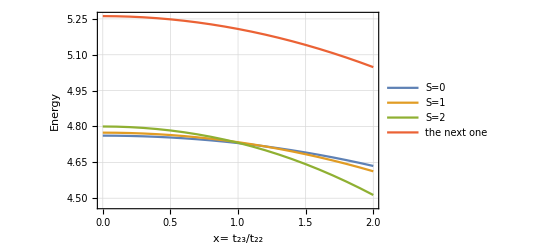

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

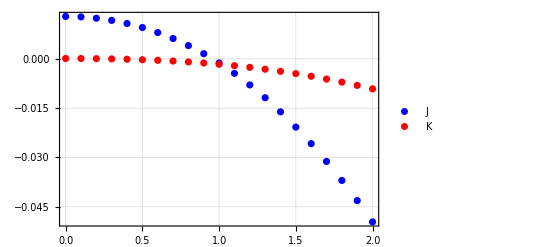

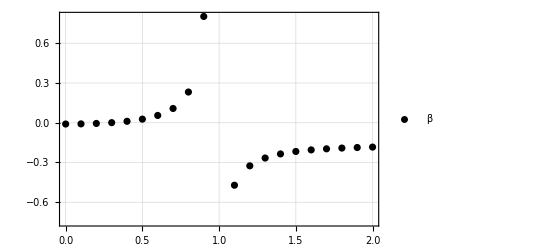

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```